## Investigating a Claim about Joint Distributions

## Simulation Approach

This content will make more sense if read in conjunction with my post of the same name.

### Step 1: Construct the random variables.

We have two discrete random variables, X and X’. X can take on values xVals = {a, b, c, d}, and X’ can take on values xprimeVals = {R, S, T, U}.

```mathematica
Clear[a,b,c,d,R,S,T];
```

```mathematica
xVals = {a,b,c};
xprimeVals = {R,S,T, U};
```

Joint probabilities of [X,X’] can then be defined on the following combinations of X and X’. Here are all possible outcomes of X,X’.

```mathematica
jointOutcomeSpace = Tuples[{xVals,xprimeVals}]
```

{{a,R},{a,S},{a,T},{a,U},{b,R},{b,S},{b,T},{b,U},{c,R},{c,S},{c,T},{c,U}}

When there are 3 values for X and 4 values for X’, the number of joint outcomes is 3 times 4 = 12. In general, the total number of distinct joint outcomes will be the number of possible outcomes for X multiplied by the number of possible outcomes for X’. We know that at the end of the day, the probability of each of the outcomes above will be 1/12th -- i.e. [X,X’] is uniformly distributed.

### Step 2: Assign X an arbitrary non-uniform discrete distribution.

Let pa be the probability of the outcome a, pb the probability of the outcome b and so on. Let’s pick some arbitraty values for pa, pb, pc, and pd.

```mathematica
pa = 0.2; pb = 0.3; pc = 0.5;
```

### Step 3: Simulate the Outcomes of X

We know the probabilities for outcomes a, b, and c (we picked these arbitrarily). Let’s generate a set of 20,000 outcomes of X. This will be the yardstick against which we measure the claim.

```mathematica
nTrials = 20000;
```

```mathematica
xOutcomes = RandomChoice[{pa, pb, pc} -> xVals, nTrials];
```

xOutcomes now holds the results of the 20,000 trials -- in other words, it is a list that has 20,000 elements where each element can be an a, b, c, or d. Here are the first 20 elements of that list:

```mathematica
Take[xOutcomes, 20]
```

{b,c,c,a,c,c,a,a,a,c,c,a,b,c,c,b,c,c,b,b}

### Step 4: Generate Candidate Probabilities for X’

According to Colbeck and Renner’s claim, there is some distribution of the outcomes of X’ such that the resulting joint distribution is uniform. So, in keeping with our simulation approach, let’s generate a bunch of 4-tuples of reals between 0 and 1 such that for every 4-tuple, its values add up to 1. We can use each of these 4-tuples to generate a set of 20,000 outcomes for X’.

```mathematica
genSingleTuple[tupleSize_, tupleSum_] := Module[{firstN, firstNTotal, outputTuple},
(* tuple size is self explanatory *)
(* tupleSum is the total to which the elements of the tuple should sum to *)
(* For most purposes, this sum will be 100 as in 100% *)
(* CAUTION: The function will return {} if the random numbers don't pan out. If that happens, try again! *)

(* Generate the n-1 tuple *)
firstN = RandomInteger[tupleSum,tupleSize - 1];
firstNTotal = Total[firstN];
If[firstNTotal ≤ tupleSum, outputTuple = Append[firstN, tupleSum-firstNTotal], outputTuple = {}]
];
```

```mathematica
genSingleTuple[3,100]
```

{88,11,1}

```mathematica
genMultipleTuples[tupleSize_, tupleSum_, numTuples_]:= Module[{},
(* NOTE: Because some of the tuples generated by genSingleTuple will be {}, numTuples should be a much larger number than the actual number of tuples that are required. Think of numTuples as the maximum possible tuples that can be generated but usually the actual number will be much less. *)
Table[genSingleTuple[tupleSize, tupleSum], numTuples] /. {} -> Sequence[]
];
```

Generate 300,000 X’ candidate distribution -- there will be a lot of them that don’t add to the total value that will have been thrown out.

```mathematica
xprimeTuples = DeleteDuplicates[genMultipleTuples[4,100,300000]];
```

```mathematica
Length[xprimeTuples]
```

44620

```mathematica
Take[xprimeTuples,10]
```

{{25,36,23,16},{35,23,34,8},{18,34,47,1},{5,36,9,50},{19,5,9,67},{22,0,42,36},{47,1,44,8},{22,16,19,43},{38,20,25,17},{56,2,33,9}}

Let’s check on how these xprimeTuples are distributed. Ideally, each element of the tuple should be uniformly distributed from 1 to 100.

What’s the distribution of the each of the elements of the tuples?

```mathematica
{t1, t2, t3, t4} = Transpose[xprimeTuples];
```

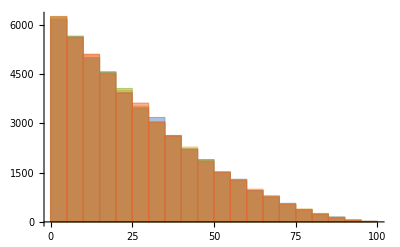

```mathematica
dt = Histogram[{t1,t2,t3,t4}]
```

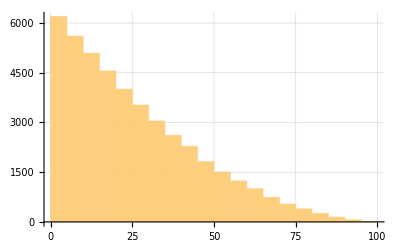

```mathematica
dt1 = Histogram[t1,GridLines->Automatic]
```

Each element is distributed similarly, but he distribution is far from uniform: there are many more smaller values than there are larger values at any location of the tuple.

This distribution makes sense; if you want four values to add to 100, and each value is obtained from a uniform distribution of integers between and including 1 and 100, then the frequencies of values greater than or equal to 40 should fall away as we see in the histogram above.

Now, let’s convert these to probabilities.

```mathematica
xprimeProbs = #/100. & /@ xprimeTuples;
```

```mathematica
Take[xprimeProbs, -10]
```

{{0.11,0.04,0.5,0.35},{0.09,0.05,0.52,0.34},{0.04,0.07,0.21,0.68},{0.1,0.16,0.18,0.56},{0.3,0.18,0.42,0.1},{0.2,0.03,0.06,0.71},{0.01,0.4,0.05,0.54},{0.24,0.,0.58,0.18},{0.05,0.03,0.85,0.07},{0.1,0.28,0.33,0.29}}

OK, we’re ready to test each of these distributions.

## Testing

For the testing phase, we’ll pretend as if the {a, b, c}’s are in one urn and the {R, S, T, U}’s are in another urn. The tokens in each urn are distributed according to the given distributions - the one for the first urn will remain the same throughout; the one for the second urn will change as we try each of the distributions we’ve manufactured in xprimeProbs.

```mathematica
urn1Population = xOutcomes;
```

```mathematica
(* CAUTION: This creates about 10,000 sets of 20,000 xprimeVals - WOW! *)
(* The complete xprimeProbs contains about 52,000 elements *)
urn2Populations= RandomChoice[# -> xprimeVals, nTrials] & /@ Take[xprimeProbs, 10000];
```

Now randomly choose 1 token from urn 1 and 1 token from urn 2; do this 10,000 times and see what the joint distribution is. And do this for every candidate distribution we’ve generated for X’.

CAUTION: This is a time-consuming command to run. To keep it simple, use a small nDistsToTry. This will make the results you see here different from the ones you’ll see in the post. The results for the post used nDistsToTry = 10,000.

```mathematica
nDistsToTry = 100;
testDistributions = Table[(Count[Table[{RandomChoice[xOutcomes], RandomChoice[urn2Populations[[i]]]}, 10000], #] & /@ jointOutcomeSpace) / 10000., {i,1, nDistsToTry}];
```

```mathematica
requiredDistribution = Table[1/12., 12]
```

{0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333}

What’s the Euclidean distance between each of the testDistributions and the required Distribution?

```mathematica
euclid = EuclideanDistance[#, requiredDistribution] & /@ testDistributions;
```

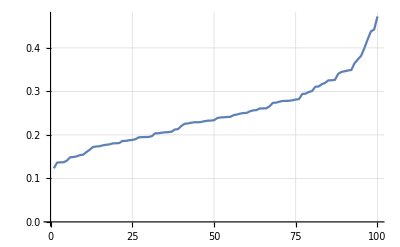

```mathematica
ListLinePlot[Sort[euclid], GridLines->Automatic]
```

There are a range of distances and some of them are quite close. Let’s see which xprimeProbs result in low distances.

```mathematica
minED = Min[euclid]
```

0.123194

```mathematica
minxprimeProbs = xprimeProbs[[Flatten[Position[euclid, minED]]]]
```

{{0.31,0.21,0.28,0.2}}

What is the distribution of [X,X’] for this candidate distribution of X’?

```mathematica
minJointDist = testDistributions[[Flatten[Position[euclid, minED]]]]
```

{{0.0603,0.0417,0.053,0.0411,0.0981,0.0613,0.0824,0.0567,0.1554,0.1099,0.132,0.1063}}

What we really need is the uniform distribution for [X,X’] which is:

```mathematica
Table[1/12., 12]
```

{0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333}

```mathematica
minPlusProbs = xprimeProbs[[Flatten[Position[euclid, x_ /; x ≥ minED && x≤ minED+0.01]]]]
```

{{0.31,0.21,0.28,0.2}}

The distributions we get for X’ distributions that are a bit greater than the minimum Euclidean distance.

```mathematica
minPlusJointDists = testDistributions[[Flatten[Position[xprimeProbs, #]]]] & /@ minPlusProbs
```

{{{0.0603,0.0417,0.053,0.0411,0.0981,0.0613,0.0824,0.0567,0.1554,0.1099,0.132,0.1063}}}

Still quite far away from a uniform distributin for [X,X’]

## Conclusion and Caveats

The simulation approach we’ve taken is limited and nothing definitive can be said (without a lot more work) about the truth of Colbeck and Renner’s claim. However, the simulations do give us a feel for how the distributions behave in the simple case that we’ve considered where X has the outcomes {a, b, c, d} and X’ has the outcomes {R, S, T, U}. Based on our evidence it doesn’t seem likely that there is an X’ distribution that will make the joint distribution of XX’ uniform. Clearly, an uniform distribution for X’ isn’t the solution, nor are any of the 7,250 or so other distributions we’ve tried. 

Therefore, for the simple case we’ve constructed, the evidence generated by the simulations points to the claim being false. The best cases for constructing the X’ probabilities is to keep them balanced and roughly equal (but making them exactly equal is not a solution).  And given the pattern we’ve seen developing with the distances, it would be surprising to see how increasing the number of outcomes of X or of X’ will make it any better for the claim.

That said, our conclusion is still tentative and might be wrong as we mentioned right up front for one or more of the following reasons: (1) We misinterpreted what Colbeck and Renner mean by the joint probability distribution of XX’, or (2) The set of candidates we generated for the X’ distributions is not representative or simply didn’t include the distribution that would have satisfied the claim. This might be the case because there might be something amiss in the procedure for converting a randomly generated 4-tuple of Reals between 0 and 1 into a 4-tuple that meets the condition of a probability distribution -- i.e. that the sum of the elements of the 4-tuple add exactly to 1.

Nevertheless, our simulations have given us some important information about how joint probability distributions behave.